```mathematica
list = Import[NotebookDirectory[]<>"out_f.sgo","Table"];
Length[list]
```

250

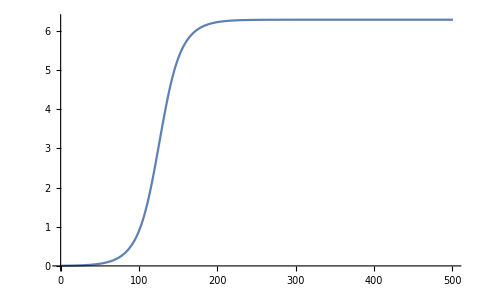

```mathematica
ListLinePlot[list[[1]],PlotRange->All]
```

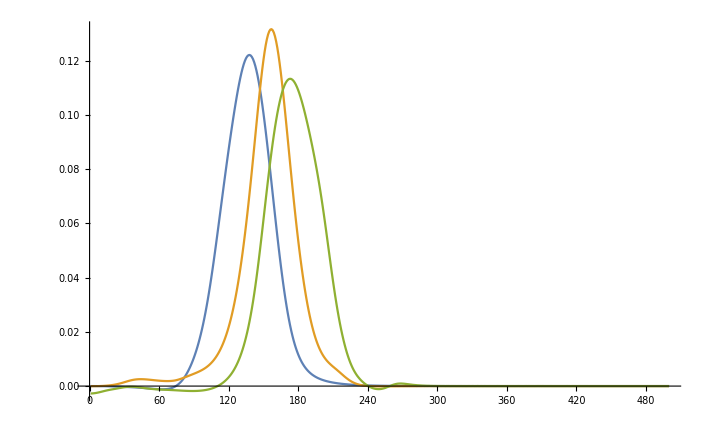

```mathematica
ListLinePlot[{Differences[list[[50]]],Differences[list[[150]]],Differences[list[[250]]]},PlotRange->Full]
```